MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

{TripleCross,Y,UpTriangle,UpTriangleTruncated,DownTriangle,DownTriangleTruncated,LeftTriangle,LeftTriangleTruncated,RightTriangle,RightTriangleTruncated,ThreePointedStar,Cross,DiagonalCross,Diamond,Square,FourPointedStar,DiagonalFourPointedStar,FivefoldCross,Pentagon,FivePointedStar,FivePointedStarThick,SixfoldCross,Hexagon,SixPointedStar,SixPointedStarSlim,SevenfoldCross,SevenPointedStar,SevenPointedStarNeat,SevenPointedStarSlim,EightfoldCross,Disk,H,I,N,Z,S,Sw,Sl}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→10,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

SetOptions::optnf: Joined is not a known option for Plot.

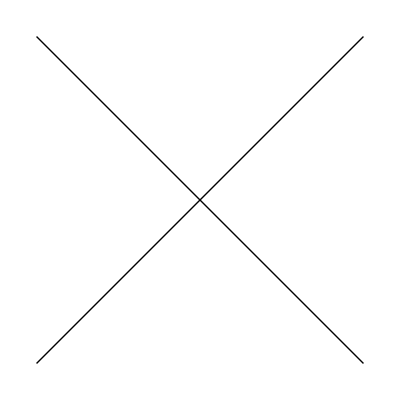
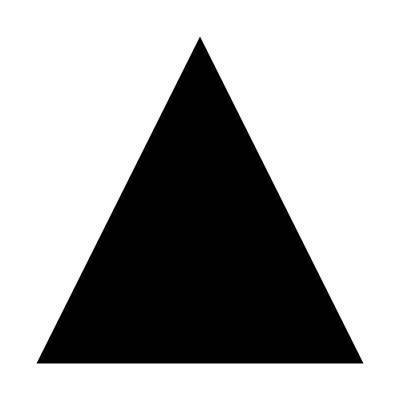
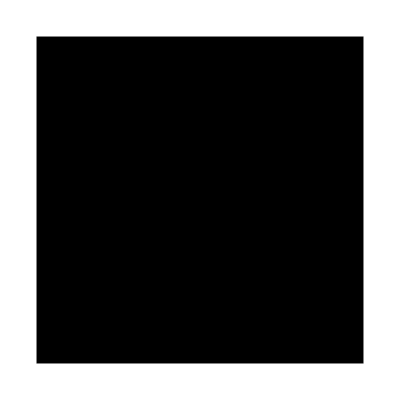
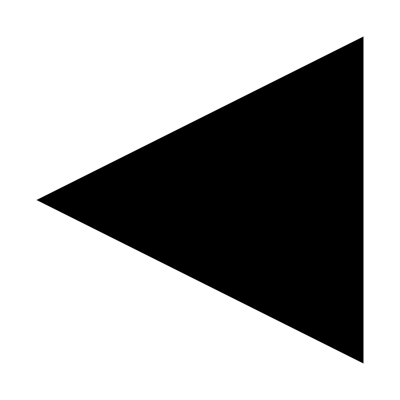
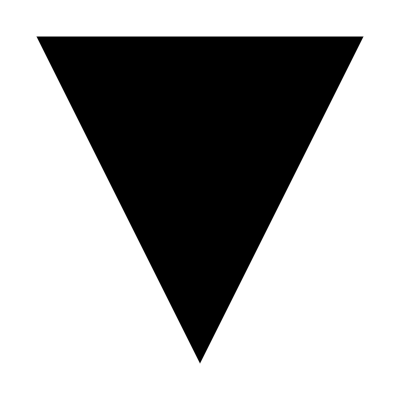
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage[rgb,dvipsnames]{xcolor},\definecolor{myred}{rgb}{0.9176470588, 0.2588235294, 0.2078431373},\definecolor{myblue}{rgb}{0.2745098039, 0.5333333333, 0.9450980392},\definecolor{myyellow}{rgb}{0.9764705882, 0.7333333333, 0.1764705882},\definecolor{mygreen}{rgb}{0.2039215686, 0.662745098, 0.3176470588}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→10,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
<<MaTeX`
<<PolygonPlotMarkers`

myblue=RGBColor[0.2745098039,0.5333333333,0.9450980392];
myred=RGBColor[0.9176470588,0.2588235294,0.2078431373];
mygreen=RGBColor[0.2039215686,0.662745098,0.3176470588];
myyellow=RGBColor[0.9764705882,0.7333333333,0.1764705882];
mygray=RGBColor[109/255//N,109/255//N,109/255//N];
mylightgray=RGBColor[185/255//N,185/255//N,185/255//N];
thickness=0.002;
size=0.05;
font="Latin Modern Roman";
imagSize=200;
fontSize=10;
markersize=0.025;
cm=72/2.54;

ts=0.02*{1,1/GoldenRatio};

fm[name_,size_:4]:=Graphics[{EdgeForm[],PolygonMarker[name,Offset[size]]},AlignmentPoint->{0,0}];

fm2[name_,size_:3]:=Graphics[{EdgeForm[],PolygonMarker[name,Offset[size]]},AlignmentPoint->{0,0}];

allShapes=PolygonMarker[All]
Tooltip[Graphics[{FaceForm[Hue@Random[]],EdgeForm[{Black,Thickness[0.003],JoinForm["Miter"]}],PolygonMarker[#,1]},ImageSize->30,PlotRange->1.5,PlotRangePadding->0,ImagePadding->0],#]&/@allShapes

fm[name_,size_:5]:=Graphics[{EdgeForm[],PolygonMarker[name,Offset[size]]},AlignmentPoint->{0,0}];

fm2[name_,size_:3]:=Graphics[{EdgeForm[],PolygonMarker[name,Offset[size]]},AlignmentPoint->{0,0}];

GetScaledLogTicks[min_,max_,scale_]:=Module[{ticks},ticks=#[Log[min],Log[max]]&/@{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]};
(*scale the tick length*)Table[{Exp[#[[1]]],#[[2]],scale*#[[3]]}&/@ticks[[i]],{i,2}]]

SetOptions[MaTeX,FontSize->fontSize]

SetOptions[ListPlot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],Frame->True,Axes->False,FrameTicksStyle->Black,Joined->True,PlotMarkers->Automatic];

SetOptions[Plot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black,Directive[Black,AbsoluteThickness[0.5]]],Frame->True,Axes->False,FrameTicksStyle->Black,Joined->True,PlotMarkers->Automatic];

SetOptions[ListLogLogPlot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],Frame->True,Axes->False,FrameTicksStyle->Black,Joined->True,PlotMarkers->Automatic];

align = Sequence[AlignmentPoint -> {0, 0}, AxesOrigin -> {0, 0}, BaselinePosition -> Axis];
size = Sequence[PlotRange -> {{-2, 2}, {-2, 2}}, PlotRangePadding -> Scaled[edgeThickness/2 + plotRangePadding], ImagePadding -> 0, ImageMargins -> 0];
plotRangePadding = .01;
edgeThickness = .1;
size = Sequence[PlotRange -> {{-2, 2}, {-2, 2}}, PlotRangePadding -> Scaled[edgeThickness/2 + plotRangePadding], ImagePadding -> 0, ImageMargins -> 0];
halfTr = {Graphics[{EdgeForm[{mygray, AbsoluteThickness[edgeThickness], JoinForm["Round"]}], Line[{{-1, -1}, {1, 1}}], Line[{{-1, 1}, {1, -1}}](*EdgeForm[],FaceForm[Opacity[1]],Polygon[{{0,2},{2/Sqrt[3],0},{-(2/Sqrt[3]),0}}],EdgeForm[{Opacity[1],Thickness[edgeThickness],JoinForm["Round"]}],FaceForm[],Polygon[{{0,2},{Sqrt[3],-1},{-Sqrt[3],-1}}]*)}, align,PlotRangePadding->0,ImagePadding->0],
   Graphics[{EdgeForm[{mygray, AbsoluteThickness[edgeThickness], JoinForm["Round"]}], Polygon[{{0, 1}, {1, -1}, {-1, -1}}]}, align,PlotRangePadding->0,ImagePadding->0],
   Graphics[{EdgeForm[{mygray, AbsoluteThickness[edgeThickness], JoinForm["Round"]}], Rectangle[{-1, -1}, {1, 1}]}, align,PlotRangePadding->0,ImagePadding->0]};
halfTr = Flatten[{halfTr, Table[halfTr /. p : {_?NumericQ, _?NumericQ} :> RotationMatrix[θ].p, {θ, {Pi/2,  Pi}}]}, 2] /. "size" -> size
Magnify[#, .1] & /@ halfTr;
ListPlot[Flatten[Table[{{n, y}}, {y, Range[1, 3]}, {n, 20}], 1], PlotMarkers -> Table[{s, 0.07}, {s, halfTr}], PlotStyle -> ColorData[60, "ColorList"], GridLines -> {Range[20], Range[3]}, PlotRange -> {{0, 21}, {0, 4}}, Axes -> False, Frame -> True];

new={{"GoogleGradient","",{}},{"Gradients"},1,{0,1},{myblue,Lighter[myblue,.5],Lighter[myblue,.75],White,Lighter[myred,.75],Lighter[myred,.5],myred},""};
ColorData["GoogleGradient"]//Quiet;
AppendTo[DataPaclets`ColorDataDump`colorSchemes,new];
AppendTo[DataPaclets`ColorDataDump`colorSchemeNames,new[[1,1]]];

new={{"GoogleGradientRev","",{}},{"Gradients"},1,{0,1},Reverse[{myblue,Lighter[myblue,.5],Lighter[myblue,.75],White,Lighter[myred,.75],Lighter[myred,.5],myred}],""};
ColorData["GoogleGradientRev"]//Quiet;
AppendTo[DataPaclets`ColorDataDump`colorSchemes,new];
AppendTo[DataPaclets`ColorDataDump`colorSchemeNames,new[[1,1]]];
SetOptions[MaTeX,"Preamble"->{"\\usepackage[rgb,dvipsnames]{xcolor}","\\definecolor{myred}{rgb}{0.9176470588, 0.2588235294, 0.2078431373}","\\definecolor{myblue}{rgb}{0.2745098039, 0.5333333333, 0.9450980392}","\\definecolor{myyellow}{rgb}{0.9764705882, 0.7333333333, 0.1764705882}","\\definecolor{mygreen}{rgb}{0.2039215686, 0.662745098, 0.3176470588}"}]
```

```mathematica
tu=Tuples[{0,1},3];
tu=Join[tu,tu];
tu=Join[tu,tu];
arr=Partition[tu,4];
dims=Dimensions[arr];

tp = arr;

Image[tp,ColorSpace->"RGB"]
tp=Transpose[tp,(trp={1,3,2})];
tpdims=Dimensions[tp];
{u,s,v}=SingularValueDecomposition[ArrayReshape[tp,{tpdims[[1]]tpdims[[2]],tpdims[[3]]}]//N,1];
dec=ArrayReshape[u.s.(v†),tpdims];
Image[Transpose[dec,trp],ColorSpace->"RGB"]

{u,s,v}=SingularValueDecomposition[ArrayReshape[arr,{dims[[1]]*dims[[2]],dims[[3]]}]//N,1];
dec=ArrayReshape[u.s.(v†),dims];
Image[dec,ColorSpace->"RGB"]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/andreas/Desktop

```mathematica
img=Import["svd_pic.jpeg",ColorSpace->"RGB"];
arr=ImageData[img];
dims=Dimensions[arr];
(*Export["i_original.jpeg",img];*)

(*
{u,s,v}=SingularValueDecomposition[ArrayReshape[arr,{dims[[1]]*dims[[2]],dims[[3]]}]//N,strunc=1];
dec=ArrayReshape[u[[;;,;;strunc]].s[[;;strunc,;;strunc]].(v†)[[;;strunc,;;]],dims];
img=Image[dec,ColorSpace->"RGB"]
Export["i_grayscale.jpeg",img]
*)

{u,s,v}=SingularValueDecomposition[ArrayReshape[arr,{dims[[1]],dims[[2]]*dims[[3]]}]//N];
strunc=Min[Dimensions[s]];
dec=ArrayReshape[u.s.(v†),dims];
img=Image[dec,ColorSpace->"RGB"];img=Show[img,ImageSize->{Automatic,156},ImagePadding->{{25,2},{20,2}}];
Export["SVD_uncompressed.png",img,ImageResolution->300]
alls=s;
```

SVD_uncompressed.png

```mathematica
strunc=260;
dec=ArrayReshape[u[[;;,;;strunc]].s[[;;strunc,;;strunc]].(v†)[[;;strunc,;;]],dims];
img=Image[dec,ColorSpace->"RGB"];
img=Show[img,ImageSize->{Automatic,156},ImagePadding->{{25,2},{20,2}}];
Export["SVD_compressed.png",img,ImageResolution->300]
```

SVD_compressed.png

```mathematica
strunc2=IntegerPart[strunc/4];
dec=ArrayReshape[u[[;;,;;strunc2]].s[[;;strunc2,;;strunc2]].(v†)[[;;strunc2,;;]],dims];
img=Image[dec,ColorSpace->"RGB"];
img=Show[img,ImageSize->{Automatic,156},ImagePadding->{{25,2},{20,2}}];
Export["SVD_compressed2.png",img,ImageResolution->300]
```

SVD_compressed2.png

```mathematica
strunc3=IntegerPart[strunc2/4];
dec=ArrayReshape[u[[;;,;;strunc3]].s[[;;strunc3,;;strunc3]].(v†)[[;;strunc3,;;]],dims];
img=Image[dec,ColorSpace->"RGB"];
img=Show[img,ImageSize->{Automatic,156},ImagePadding->{{25,2},{20,2}}];
Export["SVD_compressed3.png",img,ImageResolution->300]
```

SVD_compressed3.png

```mathematica
strunc4=IntegerPart[strunc3/4];
dec=ArrayReshape[u[[;;,;;strunc4]].s[[;;strunc4,;;strunc4]].(v†)[[;;strunc4,;;]],dims];
img=Image[dec,ColorSpace->"RGB"];
img=Show[img,ImageSize->{Automatic,156},ImagePadding->{{25,2},{20,2}}];
Export["SVD_compressed4.png",img,ImageResolution->300]
```

SVD_compressed4.png

```mathematica
dims
```

{3024,2276,3}

```mathematica
ratio[ny_,nx_,m_]:=((nx+ny+1)m)/(nx*ny)
```

```mathematica
ratio[dims[[1]],dims[[2]],strunc]//N
```

0.200252

```mathematica
pts=ts;
ts=244/110*ts;
ticks={{Join[Table[{10^i,If[i<3,Rotate[MaTeX["10^{"<>ToString[IntegerPart[Round[i]//N]]<>"}"],π/2],""],ts},{i,{-1,0,1,2,3}}],Table[{10^-i,"",0.5ts},{i,4,18,4}],{{10^3,Rotate[MaTeX["S_k"],π/2],0*ts}}],{}},{Join[Table[{10^i,If[i<3,MaTeX["10^{"<>ToString[IntegerPart[i]]<>"}"],""],ts},{i,0,6,1}],{{10^3,MaTeX["k"],.0}}],{}}}; 
ts=pts;
```

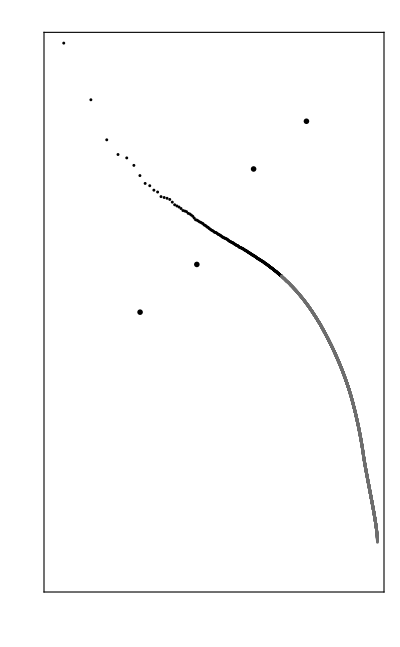

```mathematica
plot=ListLogLogPlot[{Table[{i,Diagonal[alls][[i]]},{i,strunc}],Table[{i,Diagonal[alls][[i]]},{i,strunc+1,Length[alls]}]},Joined->False,PlotMarkers->{"●",3},PlotStyle->{Black,mygray},PlotRange->Full,FrameTicks->ticks,AspectRatio->GoldenRatio,GridLines->{{{strunc,Directive[Black,Opacity[1]]},{strunc2,Directive[Black,Opacity[1]]},{strunc3,Directive[Black,Opacity[1]]},{strunc4,Directive[Black,Opacity[1]]}},{}},ImageSize->{Automatic,156},ImagePadding->{{25,2},{20,2}},Epilog->{Inset[MaTeX["\\rm (c)"],{6.2,6}],Inset[MaTeX["\\rm (d)"],{4.85,5}],Inset[MaTeX["\\rm (e)"],{4.85-1.45,3}],Inset[MaTeX["\\rm (f)"],{4.85-2*1.45,2}]}]
```

```mathematica
Export["beach_singular_values.png",plot,ImageResolution->1200]
```

beach_singular_values.png

```mathematica
ImageDimensions[plot]
```

{110,156}